```mathematica
U=(h1^2 mu2 (h2 (4 h1+3 h2) mu1+h1^2 mu2) ρ1+h2^2 mu1 (h2^2 mu1+h1 (3 h1+4 h2) mu2) ρ2)/(h1 (h1+h2) mu2 (h1 (4 h2 mu1+h1 mu2) ρ1+3 h2^2 mu1 ρ2))/.{mu1->1, mu2->μr, h1->1, h2->hr, ρ1->1, ρ2->ρr}//Simplify
f1=q1;
u2=((U(1+hr)-u1 h1)/(1+hr-h1))
```

(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/((1+hr) μr (4 hr+μr+3 hr^2 ρr))

(-h1 u1+(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr)))/(1-h1+hr)

```mathematica
beta1=(6 (h1^2 (16 h2^2 mu1^2+7 h1 h2 mu1 mu2+h1^2 mu2^2) ρ1^2+5 h1 h2^2 mu1 (5 h2 mu1+h1 mu2) ρ1 ρ2+10 h2^4 mu1^2 ρ2^2))/(5 (h1 (4 h2 mu1+h1 mu2) ρ1+3 h2^2 mu1 ρ2)^2)/.{h2->(1+hr-h1), ρ1->1, ρ2->ρr, mu1->1, mu2->μr}//Simplify
beta2=(6 (10 h1^4 mu2^2 ρ1^2+5 h1^2 h2 mu2 (h2 mu1+5 h1 mu2) ρ1 ρ2+h2^2 (h2^2 mu1^2+7 h1 h2 mu1 mu2+16 h1^2 mu2^2) ρ2^2))/(5 (3 h1^2 mu2 ρ1+h2 (h2 mu1+4 h1 mu2) ρ2)^2)/.{h2->(1+hr-h1), ρ1->1, ρ2->ρr, mu1->1, mu2->μr}//Simplify
```

(6 (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2))/(5 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2)

(6 (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2))/(5 (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2)

```mathematica
f2=((beta1 u1^2 h1-beta2 u2^2 (1+hr-h1)+((1-ρr)(1/Fr1^2) h1^2)/2)/(1+ρr))//.{u1->{q1/h1}, u2->((U(1+hr)-u1 h1)/(1+hr-h1))}
```

{1/(1+ρr)((h1^2 (1-ρr))/(2 Fr1^2)+(6 q1^2 (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2))/(5 h1 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2)-(6 (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (-q1+(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr)))^2)/(5 (1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2))}

```mathematica
f2Simp=Assuming[{h1∈PositiveReals  && q1∈PositiveReals && hr∈PositiveReals  && ρr∈PositiveReals  && μr∈PositiveReals}, Simplify[f2]][[1]]
```

1/(1+ρr)(-(h1^2 (-1+ρr))/(2 Fr1^2)+(6 q1^2 (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2))/(5 h1 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2)-(6 (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (q1-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr)))^2)/(5 (1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2))

```mathematica
m11=D[f1, h1]//Simplify
```

0

```mathematica
m12=D[f1, q1]//Simplify
```

1

```mathematica
m21=D[f2Simp, h1]
```

1/(1+ρr)(-(h1 (-1+ρr))/Fr1^2+(6 q1^2 (h1^2 (-32 (1-h1+hr)-7 h1 μr+7 (1-h1+hr) μr+2 h1 μr^2)+2 h1 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)-10 h1 (1-h1+hr) (5 (1+hr)+h1 (-5+μr)) ρr+5 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+5 h1 (1-h1+hr)^2 (-5+μr) ρr-40 (1-h1+hr)^3 ρr^2))/(5 h1 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2)-(12 q1^2 (4 (1+hr)+2 h1 (-4+μr)-6 (1-h1+hr) ρr) (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2))/(5 h1 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^3)-(6 q1^2 (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2))/(5 h1^2 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2)-(6 (40 h1^3 μr^2+5 h1^2 (1-h1+hr) μr (-1+5 μr) ρr-5 h1^2 μr (1+hr+h1 (-1+5 μr)) ρr+10 h1 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 (-2 (1-h1+hr)-7 h1 μr+7 (1-h1+hr) μr+32 h1 μr^2) ρr^2-2 (1-h1+hr) ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (q1-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr)))^2)/(5 (1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2)+(12 (6 h1 μr+(1-h1+hr) (-1+4 μr) ρr-(1+hr+h1 (-1+4 μr)) ρr) (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (q1-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr)))^2)/(5 (1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^3)-(6 (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (q1-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr)))^2)/(5 (1-h1+hr)^2 (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2))

```mathematica
m22=D[f2Simp, q1]//Simplify
```

1/(5 (1+ρr))12 ((q1 (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2))/(h1 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2)-((10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (q1-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr))))/((1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2))

```mathematica
jacMat=({{m11, m12}, {m21, m22}});
```

```mathematica
u1Equil=(-((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))));
```

```mathematica
jacMatMod=jacMat/.{q1->(u1Equil h1)}
```

{{0,1},{1/(1+ρr)(-(h1 (-1+ρr))/Fr1^2+(6 h1 (h1^2 (-32 (1-h1+hr)-7 h1 μr+7 (1-h1+hr) μr+2 h1 μr^2)+2 h1 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)-10 h1 (1-h1+hr) (5 (1+hr)+h1 (-5+μr)) ρr+5 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+5 h1 (1-h1+hr)^2 (-5+μr) ρr-40 (1-h1+hr)^3 ρr^2) ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2)/(5 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2 (-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2)-(12 h1 (4 (1+hr)+2 h1 (-4+μr)-6 (1-h1+hr) ρr) (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2) ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2)/(5 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^3 (-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2)-(6 (h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2) ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2)/(5 (h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2 (-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2)-(6 (40 h1^3 μr^2+5 h1^2 (1-h1+hr) μr (-1+5 μr) ρr-5 h1^2 μr (1+hr+h1 (-1+5 μr)) ρr+10 h1 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 (-2 (1-h1+hr)-7 h1 μr+7 (1-h1+hr) μr+32 h1 μr^2) ρr^2-2 (1-h1+hr) ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr))-(h1 ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))^2)/(5 (1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2)+(12 (6 h1 μr+(1-h1+hr) (-1+4 μr) ρr-(1+hr+h1 (-1+4 μr)) ρr) (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr))-(h1 ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))^2)/(5 (1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^3)-(6 (10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr))-(h1 ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))^2)/(5 (1-h1+hr)^2 (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2)),1/(5 (1+ρr))12 (-(((h1^2 (16 (1-h1+hr)^2+7 h1 (1-h1+hr) μr+h1^2 μr^2)+5 h1 (1-h1+hr)^2 (5 (1+hr)+h1 (-5+μr)) ρr+10 (1-h1+hr)^4 ρr^2) ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/((h1 (4 (1+hr)+h1 (-4+μr))+3 (1-h1+hr)^2 ρr)^2 (-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))))-((10 h1^4 μr^2+5 h1^2 (1-h1+hr) μr (1+hr+h1 (-1+5 μr)) ρr+(1-h1+hr)^2 ((1-h1+hr)^2+7 h1 (1-h1+hr) μr+16 h1^2 μr^2) ρr^2) (-(μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr)/(μr (4 hr+μr+3 hr^2 ρr))-(h1 ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))))/((1-h1+hr) (3 h1^2 μr+(1-h1+hr) (1+hr+h1 (-1+4 μr)) ρr)^2))}}

```mathematica
lambdaHat=(-((h1 (-(((1-h1+hr+h1 μr) ρr (6 h1 μr+(1-h1+hr) (-1+4 μr) ρr-(1-h1+hr+4 h1 μr) ρr) (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)^2))+((-1+μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr)^2 (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))+(h1 (((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr) (4 (1-h1+hr)+h1 (-4+μr)+h1 μr-6 (1-h1+hr) ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr)^2)-((-1+μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))+(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr) (6 h1 μr+(1-h1+hr) (-1+4 μr) ρr-(1-h1+hr+4 h1 μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)^2)-(h1 (-1+μr) μr ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr)^2 (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))-(μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))) ((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))^2-((1-hr ρr)/Fr1^2+((1-h1+hr+h1 μr) ρr (μr (hr (4+3 hr)+μr)+hr^2 (hr^2+3 μr+4 hr μr) ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr)))/(-((1-h1+hr+h1 μr) (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (hr+μr) (h1 (4 (1-h1+hr)+h1 μr)+3 (1-h1+hr)^2 ρr))-(h1 μr (1-h1+hr+h1 μr) ρr (4 hr+μr+3 hr^2 ρr))/(Fr1^2 (1-h1+hr) (hr+μr) (3 h1^2 μr+(1-h1+hr) (1-h1+hr+4 h1 μr) ρr))));
```

```mathematica
Eigenvalues[jacMatMod/.{μr->0.50, ρr->0.70, hr->0.50, Fr1->1.0, h1->1.0 }]
```

{1.97088,0.558558}

```mathematica
jacMatMod/.{μr->0.50, ρr->0.70, hr->0.50, Fr1->1.0, h1->1.0 }
```

{{0,1},{-1.10085,2.52944}}

```mathematica
Dimensions[jacMatMod]
```

{2,2}

```mathematica
Dimensions[jacMatMod/.{μr->0.50, ρr->0.70, hr->0.50, Fr1->1.0, h1->1.0 }]
```

{2,2}

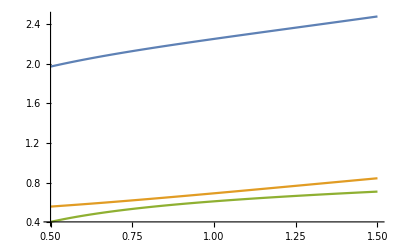

```mathematica
Plot[{Eigenvalues[jacMatMod/.{μr->0.50, ρr->0.70, Fr1->1.0, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.50, ρr->0.70, Fr1->1.0, h1->1.0 }][[2]], lambdaHat/.{μr->0.50, ρr->0.70, Fr1->1.0, h1->1.0 }}, {hr,0.5,1.5}]
```

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
(* improved figure *)
```

```mathematica
tickSpecification=Table[{i,i},{i,{0.1,1,2,3,4,5}}]
```

{{0.1,0.1},{1,1},{2,2},{3,3},{4,4},{5,5}}

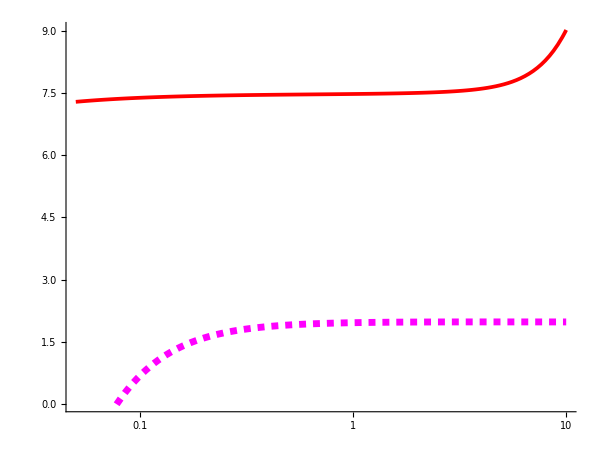

```mathematica
(* Case: μr=0.02, ρr=0.001, Fr1=0.2 *)
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->0.20, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->0.20, h1->1.0 }][[2]], lambdaHat/.{μr->0.02, ρr->0.001, Fr1->0.20, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{Automatic,{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->120,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

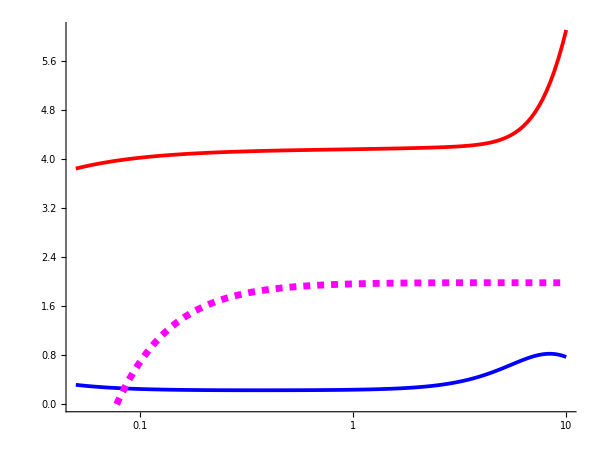

```mathematica
(* Case: μr=0.02, ρr=0.001, Fr1=1.0 *)
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->1.0, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->1.0, h1->1.0 }][[2]], lambdaHat/.{μr->0.02, ρr->0.001, Fr1->1.0, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

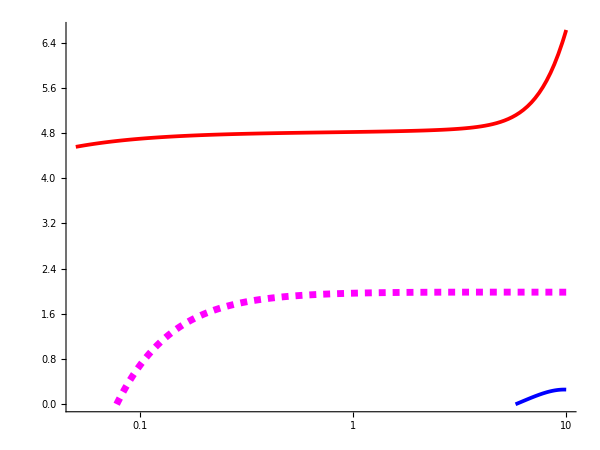

```mathematica
(* Case: μr=0.02, ρr=0.001, Fr1=0.50 *)
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->0.5, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->0.5, h1->1.0 }][[2]], lambdaHat/.{μr->0.02, ρr->0.001, Fr1->0.5, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

## A larger density-viscosity ratio below

### Case: μr=0.10, ρr=0.10, Fr1=0.20

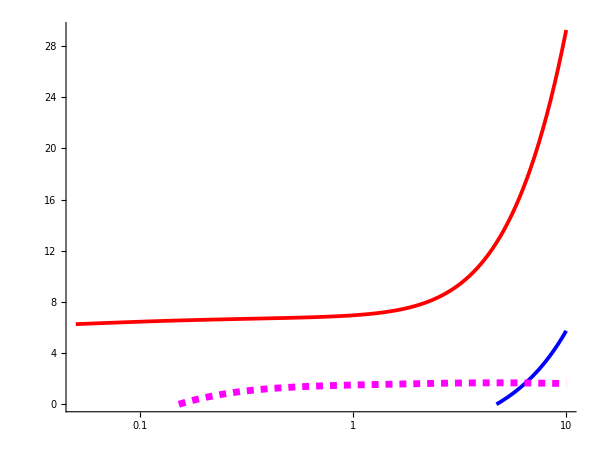

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.1, ρr->0.1, Fr1->0.20, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.1, ρr->0.1, Fr1->0.20, h1->1.0 }][[2]], lambdaHat/.{μr->0.1, ρr->0.1, Fr1->0.20, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

### Case : μr = 0.10, ρr = 0.10, Fr1 = 0.50

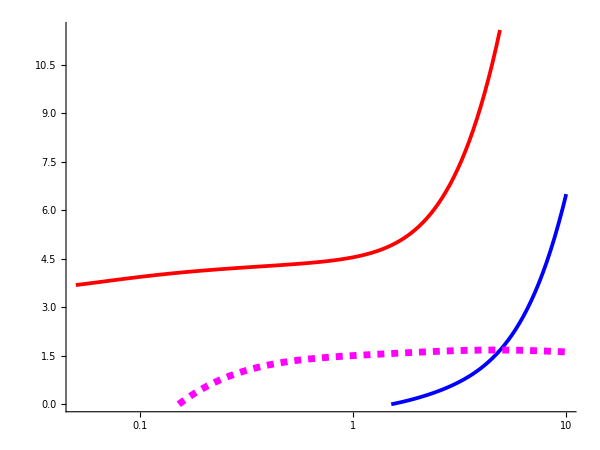

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.1, ρr->0.1, Fr1->0.50, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.1, ρr->0.1, Fr1->0.50, h1->1.0 }][[2]], lambdaHat/.{μr->0.1, ρr->0.1, Fr1->0.50, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

### Case : μr = 0.10, ρr = 0.10, Fr1 = 0.50

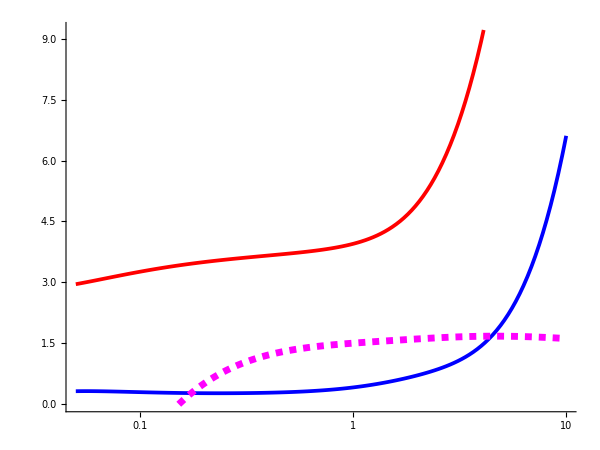

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.1, ρr->0.1, Fr1->1.0, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.1, ρr->0.1, Fr1->1.0, h1->1.0 }][[2]], lambdaHat/.{μr->0.1, ρr->0.1, Fr1->1.0, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

## A even Larger density - viscosity ratio below (nearly Boussinesq)

### Case : μr = 0.90, ρr = 0.90, Fr1 = 0.20

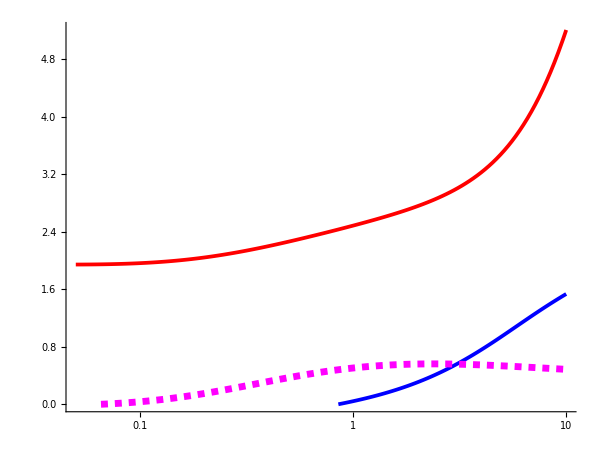

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.9, ρr->0.9, Fr1->0.20, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.9, ρr->0.9, Fr1->0.20, h1->1.0 }][[2]], lambdaHat/.{μr->0.9, ρr->0.9, Fr1->0.20, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

### Case : μr = 0.90, ρr = 0.90, Fr1 = 0.50

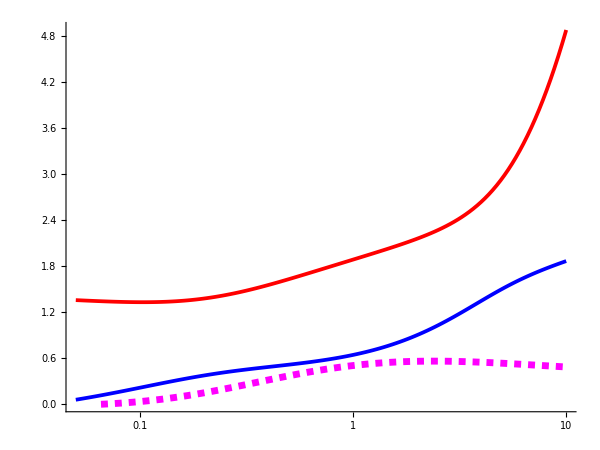

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.9, ρr->0.9, Fr1->0.50, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.9, ρr->0.9, Fr1->0.50, h1->1.0 }][[2]], lambdaHat/.{μr->0.9, ρr->0.9, Fr1->0.50, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

### Case : μr = 0.90, ρr = 0.90, Fr1 = 1.0

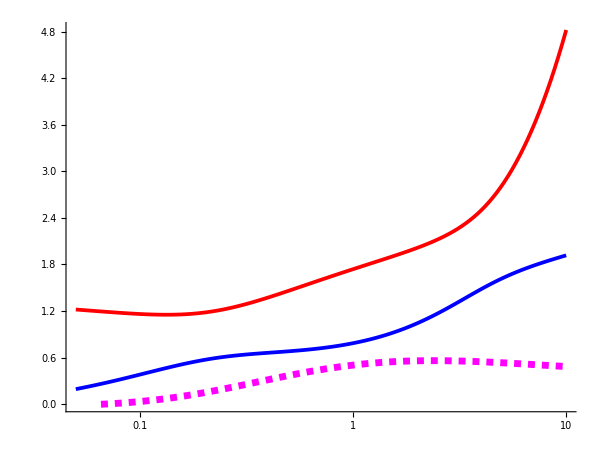

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.9, ρr->0.9, Fr1->1.0, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.9, ρr->0.9, Fr1->1.0, h1->1.0 }][[2]], lambdaHat/.{μr->0.9, ρr->0.9, Fr1->1.0, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},AxesLabel->{MaTeX["h_r",Magnification->2.1],MaTeX["\\frac{\\lambda_{\\pm}}{\\overline{U}_1},\\,\\frac{\\hat{\\lambda}}{\\overline{U}_1}", Magnification->2.0]}, PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.88, 0.75}],PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->0.75,ImageSize->600, PlotPoints->128,TicksStyle->{{FontSize->20,FontFamily->"Times"},{FontSize->20,FontFamily->"Times"}} ]
```

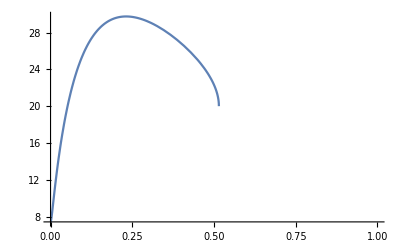

```mathematica
Plot[Eigenvalues[jacMatMod/.{μr->0.1, Fr1->0.2, h1->1.0 , hr->9.0}][[1]], {ρr,0,1}]
```

```mathematica
Using Scientific theme for plotting
```

### Case : μr = 0.02, ρr = 0.001, Fr1 = 0.2

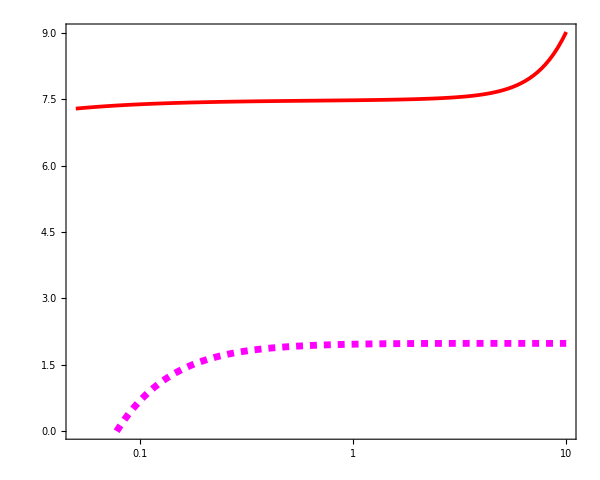

```mathematica
LogLinearPlot[{Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->0.20, h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.02, ρr->0.001, Fr1->0.20, h1->1.0 }][[2]], lambdaHat/.{μr->0.02, ρr->0.001, Fr1->0.20, h1->1.0 }}, {hr,0.05,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},FrameLabel->{MaTeX["h_r",Magnification->2.2],MaTeX["{\\lambda_{\\pm}}/{\\overline{U}_1},\\,{\\hat{\\lambda}}/{\\overline{U}_1}", Magnification->2.0]},PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.9, 0.55}],PlotRange->{{0.05,10},{0,Automatic}},AspectRatio->0.8,ImageSize->600, PlotPoints->120,FrameTicksStyle->{{FontSize->24,FontFamily->"Times"},{FontSize->24,FontFamily->"Times"}} , PlotTheme->"Scientific"]
```

### Case : μr = 0.25, ρr = 0.25, hr = 5.0

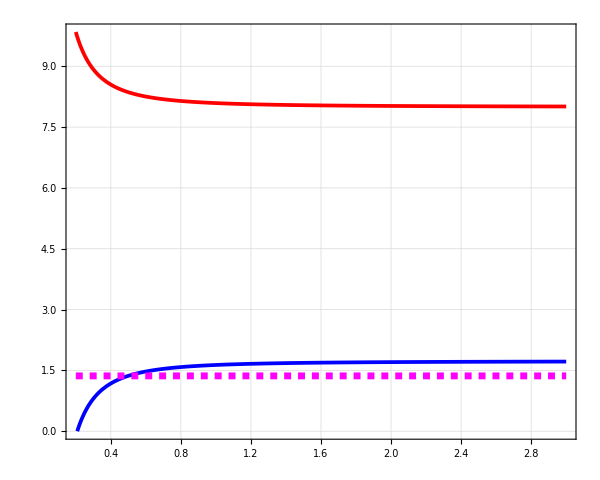

```mathematica
Plot[{Eigenvalues[jacMatMod/.{μr->0.25, ρr->0.25,hr->5.0,  h1->1.0 }][[1]], Eigenvalues[jacMatMod/.{μr->0.25, ρr->0.25,hr->5.0,  h1->1.0 }][[2]], lambdaHat/.{μr->0.25, ρr->0.25,hr->5.0,h1->1.0 }}, {Fr1,0.20,3.0},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed], PlotStyle->{{Red,Thickness[0.0045]},{Blue,Thickness[0.0045]},{Magenta,Dashed,Thickness[0.00825]}},FrameLabel->{MaTeX["{\\rm Fr}_1",Magnification->2.2],MaTeX["{\\lambda_{\\pm}}/{\\overline{U}_1},\\,{\\hat{\\lambda}}/{\\overline{U}_1}", Magnification->2.0]},PlotLegends->Placed[{MaTeX["\\frac{\\lambda_{+}}{\\overline{U}_1}",Magnification->1.95],MaTeX["\\frac{\\lambda_{-}}{\\overline{U}_1}",Magnification->1.95], MaTeX["\\frac{\\hat{\\lambda}}{\\overline{U}_1}",Magnification->1.95]}, {0.9, 0.68}],PlotRange->{{0.2,3.0},{0.0,Automatic}},AspectRatio->0.8,ImageSize->600, PlotPoints->128,FrameTicksStyle->{{FontSize->24,FontFamily->"Times"},{FontSize->24,FontFamily->"Times"}} , PlotTheme->"Scientific"]
```

```mathematica
frCoord=Table[i,{i,0.2,3,(3-2)/128.0}];
```

```mathematica
lambdaPlusVal=Table[Eigenvalues[jacMatMod/.{μr->0.25, ρr->0.25,hr->5.0,  h1->1.0, Fr1->frCoord[[i]] }][[1]],{i,1,Length[frCoord]}];
lambdaMinusVal=Table[Eigenvalues[jacMatMod/.{μr->0.25, ρr->0.25,hr->5.0,  h1->1.0, Fr1->frCoord[[i]] }][[2]],{i,1,Length[frCoord]}];
lambdaHatVal=Table[lambdaHat/.{μr->0.25, ρr->0.25,hr->5.0,h1->1.0 , Fr1->frCoord[[i]] },{i,1,Length[frCoord]}];
```

```mathematica
dat1=Flatten/@Transpose[{frCoord,lambdaPlusVal, lambdaMinusVal, lambdaHatVal}];
```

```mathematica
Export["C:\\Users\\boyuan\\Desktop\\test.txt",dat1,"Table"]
```

C:\Users\boyuan\Desktop\test.txt